# Network Map Animation Routines

## Functions

```mathematica
<<PajaroLocoPublic`
SetDirectory[NotebookDirectory[]];
ImportAndReshapeMosquitoDatasets[dataPath_,{maleFilenamePattern_,femaleFilenamePattern_}]:=Module[{names,dataSets,maleFilenames,femaleFilenames,maleDatasets,femaleDatasets,genotypes,ticksMax,maleMax,femaleMax},
maleFilenames=FileNames[maleFilenamePattern<>"_*.csv",dataPath]//Sort;
femaleFilenames=FileNames[femaleFilenamePattern<>"_Aggregate*.csv",dataPath]//Sort;
maleDatasets=AddTotalPopulationToDataset[Map[Import[#][[2;;All,2;;All]]&,maleFilenames]];
femaleDatasets=AddTotalPopulationToDataset[Map[Import[#][[2;;All,2;;All]]&,maleFilenames]];
genotypes=Import[maleFilenames[[1]]][[1,2;;All]];
ticksMax=Length[maleDatasets[[1]]];
{maleMax,femaleMax}={Flatten[maleDatasets]//Max,Flatten[femaleDatasets]//Max};
(*Output*)
{
{maleDatasets,femaleDatasets},
{genotypes,ticksMax,{maleMax,femaleMax}}
}
]
GenerateColorPalette[genotypes_,colorScheme_]:=Module[{steps,colors},
steps=(genotypes//Length)-1;
colors={ColorData[colorScheme,#]&/@Range[0,1,1/steps],Black}//Flatten;
{Append[genotypes,"Total"],colors}
]
ImportGeoCoordinatesAndKernel[coordinatesFilePath_,kernelFilePath_]:=Module[{cities,transitionsMatrix},
cities={#[[1]],{#[[2]],#[[3]]},#[[4]]}&/@Import[coordinatesFilePath];
transitionsMatrix=Import[kernelFilePath][[2;;All]];
{cities,transitionsMatrix}
]
AddTotalPopulationToDataset[dataset_]:=Table[Append[#,Total[#]]&/@dataset[[i]],{i,1,Length[dataset]}]
AggregatePopulationByGenotypeIndices[populationDatasets_,genotypesIndicesToAggregate_]:=Module[{popsDatasets,geneLabels},
popsDatasets=Table[Transpose[Total/@populationDatasets[[i,All,#[[2]]]]&/@genotypesIndicesToAggregate],{i,1,Length[populationDatasets]}];
geneLabels=genotypesIndicesToAggregate[[All,1]];
{geneLabels,AddTotalPopulationToDataset[popsDatasets]}
]
AggregatePopulationAcrossNodes[aggregatedPopulations_]:=Table[Total/@(aggregatedPopulations[[All,i]]//Transpose),{i,1,Length[aggregatedPopulations[[1]]]}]
SubsetPopulations[{aggregatedPopulations_,aggregatedPopulationsAcrossNodes_},dataRange_]:={aggregatedPopulations[[All,dataRange[[1]];;dataRange[[2]]]]//Transpose,aggregatedPopulationsAcrossNodes[[dataRange[[1]];;dataRange[[2]]]]}
GeneratePopCountsFrames[{labels_,colors_},subsetPopulationsAccrossNodes_]:=Module[{styledLabels,styledNumbers,gridFrames},
styledLabels=Style[#,30]&/@labels;
styledNumbers=Table[Style[Round[#],30,Black]&/@Threshold[i,{"Hard",10^-1}],{i,subsetPopulationsAccrossNodes}];
gridFrames=Table[
Grid[{styledLabels,styledNumbers[[i]]}//Transpose,
Frame->True,
FrameStyle->Thick,
ItemSize->10,
Background->{None,Opacity[.25,#]&/@colors},
Alignment->Center
]
,{i,1,subsetPopulationsAccrossNodes//Length}]
]
BarChartPopCountsFrames[subsetPopulations_,{colors_,maxPop_,frameDimensions_}]:=BarChart[subsetPopulations[[All,1;;(Length[labels]-1)]],
ChartLayout->"Stacked",
ChartStyle->{EdgeForm[None],(Directive[Opacity[1],#]&/@colors )},
Frame->False,
PlotRange->{{.5,Length[subsetPopulations]+.5},{0,maxPop}},
Axes->False,
PerformanceGoal->"Speed",
BarSpacing->.2,
ImagePadding->0,
AspectRatio->1/10,
BarOrigin->Top,
PlotRangePadding->{0,0},
ImageSize->frameDimensions[[1]]
]
BarChartPopDynamicsFrames[tick_,aggregatedPopulationsAcrossNodes_,{colors_,maxPop_,ticksMax_,frameDimensions_,labels_}]:=Module[{dataUntilTick},
dataUntilTick=aggregatedPopulationsAcrossNodes[[1;;tick]][[All,1;;(Length[labels]-1)]];
BarChart[dataUntilTick,
ChartLayout->"Stacked",
ChartStyle->{EdgeForm[None],(Directive[Opacity[1],#]&/@colors )},
Frame->False,
PlotRange->{{0,ticksMax},{0,maxPop}},
Axes->False,
PerformanceGoal->"Speed",
BarSpacing->{0,0},
ImagePadding->0,
AspectRatio->1/10,
BarOrigin->Bottom,
PlotRangePadding->{0,0},
ImageSize->frameDimensions[[1]]
]
]
ExportFrames[plots_,dataRange_,{outputBasePath_,outputFolder_,filesBaseName_}]:=Module[{namesStrings,pathsStrings},
namesStrings=(filesBaseName<>StringPadLeft[ToString[#],6,"0"]<>".png")&/@Range[dataRange[[1]],dataRange[[2]]];
pathsStrings=(outputBasePath<>outputFolder<>#)&/@namesStrings;
Export[#[[1]],#[[2]]]&/@Transpose[{pathsStrings,plots}]
]
BarChartPopDynamicsMaskFrames[fullRaster_,{tick_,ticksMax_}]:=Module[{rasterDimensions,stepSize,composedImage,day=tick},
rasterDimensions=ImageDimensions[fullRaster];
stepSize=rasterDimensions[[1]]/ticksMax//N;
composedImage=ImageCompose[
fullRaster,
Graphics[{
White,Opacity[1],Rectangle[{day*stepSize,0},{day*stepSize+1*stepSize,rasterDimensions[[2]]}],
White,Opacity[.75],Rectangle[{day*stepSize+1*stepSize*stepSize,0},{rasterDimensions[[1]],rasterDimensions[[2]]}],
Black,Opacity[0],Rectangle[{0,0},{rasterDimensions[[1]],rasterDimensions[[2]]}]
},
ImageSize->rasterDimensions[[1]],
AspectRatio->1/5,
ImagePadding->None,
ImageMargins->0,
PlotRangePadding->None
]
]
]
EdgesStyleList2[vertexSyllableList_,OptionsPattern[]]:=Switch[OptionValue[VariableStyle],
"LineColor",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[1*vertexSyllableList[[i]][[2]]+.01],Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"LineWidth",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.5],Blue,Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],
"Both",Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Opacity[.75*vertexSyllableList[[i]][[2]]+.05],Thickness[vertexSyllableList[[i]][[2]]*OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}],_,Table[DirectedEdge[vertexSyllableList[[i]][[1]][[1]],vertexSyllableList[[i]][[1]][[2]]]->{Thickness[OptionValue[LineThickness]]},{i,1,Length[vertexSyllableList]}]]
edgeshape[e_,___]:={Arrowheads[{{.0001,.5}}],Arrow[e]}
Options[GraphTransitionsFrequenciesWithMax]:={ImagePadding->None,Background->White,VertexStyle->Automatic,VertexCoordinates->Automatic,LineThickness->.0005,VariableStyle->"Both",GraphLayout->Automatic,ImageSize->Automatic,VertexSize->.5,EdgeShapeFunction->edgeshape,VertexLabelStyle->{Italic},Prolog->{},Epilog->{},VertexShape->Automatic}
GraphTransitionsFrequenciesWithMax[frequenciesOutput_,max_,OptionsPattern[]]:=Module[{frequencies,syllables,edges,fixedEdgesList,vertexSyllableList,normalizedVertexSyllableList,edgesStyleList,links},frequencies=frequenciesOutput[[1]];
syllables=frequenciesOutput[[2]];
edges=Table[DirectedEdge[i,j]->frequencies[[i,j]],{i,Length[syllables]},{j,Length[syllables]}]//Flatten;
fixedEdgesList=DeleteCases[edges,DirectedEdge[_,_]->0];
vertexSyllableList=VertexNumberToVertexSyllable[frequenciesOutput[[2]],fixedEdgesList];
normalizedVertexSyllableList=(DirectedEdge[#[[1]],#[[2]][[1]]]->#[[2]][[2]]/max&)/@vertexSyllableList;
edgesStyleList=EdgesStyleList2[normalizedVertexSyllableList,LineThickness->OptionValue[LineThickness],VariableStyle->OptionValue[VariableStyle]];
links=DirectedEdge[#[[1]],#[[2,1]]]&/@vertexSyllableList;
Graph[syllables,links,
EdgeWeight->vertexSyllableList[[All,2,2]],
VertexStyle->OptionValue[VertexStyle],
EdgeStyle->edgesStyleList,
VertexCoordinates->OptionValue[VertexCoordinates],
ImageSize->OptionValue[ImageSize],
GraphLayout->OptionValue[GraphLayout],
EdgeShapeFunction->OptionValue[EdgeShapeFunction],
VertexShape->OptionValue[VertexShape],
VertexSize->OptionValue[VertexSize],
AspectRatio->1,
VertexLabelStyle->OptionValue[VertexLabelStyle],
VertexLabels->Placed["Name",Center],
EdgeLabels->Table[links[[i]]->Placed[fixedEdgesList[[All,2]][[i]],Tooltip],{i,Length[links]}],
Prolog->OptionValue[Prolog],
Epilog->OptionValue[Epilog],
Background->OptionValue[Background],
ImagePadding->OptionValue[ImagePadding],
PerformanceGoal->"Speed"
]
]
CalculateNetworkParameters[cities_,transitionsMatrix_]:=Module[{range,transitionsMatrix2,vertexCoordinates,transMatrix},
range=Range[cities//Length];
transitionsMatrix2={transitionsMatrix,ToString/@range};
vertexCoordinates=cities;
transMatrix={ReplacePart[Chop[transitionsMatrix2[[1]]//UpperTriangularize],{i_,i_}->0],transitionsMatrix2[[2]]};
{range,transMatrix,vertexCoordinates}
]
CalculateVertexScalers[{range_,nodeScaler_},scaledSizesPieChartFramesAtFrame_]:=Module[{vertexShapes,vertexSizes},
vertexShapes=Flatten[{ToString[#[[1]]]->#[[2,1]]}&/@Transpose[{range,scaledSizesPieChartFramesAtFrame}]];
vertexSizes=Flatten[{ToString[#[[1]] ]->nodeScaler*#[[2,2]]}&/@Transpose[{range,scaledSizesPieChartFramesAtFrame}]];
{vertexShapes,vertexSizes}
]
GenerateNetworkFrames[vertexShapeAndSizeFrames_,{vertexCoordinates_,networkMatrix_},{edgeThreshold_,lineThickness_,frameDimensions_},countryMap_,colorPalette_]:=Module[{},
GraphTransitionsFrequenciesWithMax[networkMatrix,edgeThreshold,
VertexCoordinates->vertexCoordinates,
LineThickness->lineThickness,
VertexShape->vertexShapeAndSizeFrames[[1]],
VertexSize->vertexShapeAndSizeFrames[[2]],
VariableStyle->"LineColor",
VertexLabelStyle->Directive[Red,Italic,Opacity[0]],
ImageSize->frameDimensions[[1]],
Prolog->
{
EdgeForm[Directive[Opacity[1.0],Thickness[.065],Darker[colorPalette[[5]],.125]]],Opacity[0],colorPalette[[5]],countryMap[[2]],
EdgeForm[Directive[Opacity[1.0],Thickness[.025],colorPalette[[5]]]],Opacity[0],colorPalette[[3]],countryMap[[2]],
EdgeForm[Directive[Opacity[0.6],Thickness[.045],Lighter[colorPalette[[2]],.5]]],Opacity[0],colorPalette[[5]],countryMap[[1]]
},
ImagePadding->500
]
]
ParseFilenames[tick_,{outputFolder_,{outputPopCounts_,outputBarCharts_,outputFlow_,outputNetworks_},{baseCounts_,baseDays_,baseBarCharts_,basePopDyn_,baseNetworks_}}]:=Module[{paddedNumber,rastersFolders,rastersNames},
paddedNumber=StringPadLeft[ToString[tick],6,"0"];
rastersFolders=(outputFolder<>#)&/@{outputPopCounts,outputBarCharts,outputFlow,outputNetworks};
rastersNames=(#<>paddedNumber<>".png")&/@{baseCounts,baseDays,baseBarCharts,basePopDyn,baseNetworks};
{
rastersFolders[[1]]<>rastersNames[[1]],
rastersFolders[[1]]<>rastersNames[[2]],
rastersFolders[[2]]<>rastersNames[[3]],
rastersFolders[[3]]<>rastersNames[[4]],
rastersFolders[[4]]<>rastersNames[[5]]
}
]

GeneratePieChartsAtTick[subsetPopulation_,labels_,maxPop_]:=Module[{chartAndPop},
chartAndPop={
PieChart[#,ChartStyle->colors,BaseStyle->Directive[EdgeForm[Thickness[.07]]],ColorFunction->(EdgeForm[Black]&),PerformanceGoal->"Speed"],
Total[#]
}&/@(subsetPopulation[[All,1;;(Length[labels]-1)]]);
{#[[1]],Sqrt[#[[2]]/maxPop]}&/@chartAndPop
]
```

```mathematica
ImportGeoCoordinatesAndKernel[coordinatesFilePath_,kernelFilePath_]:=Module[{cities,transitionsMatrix},
cities={1,{#[[1]],#[[2]]},50}&/@Import[coordinatesFilePath];
transitionsMatrix=Import[kernelFilePath][[1;;All]];
{cities,transitionsMatrix}
]
```

```mathematica
rgbColors={
ColorData[{"LakeColors",{1,0}}][1],
ColorData[{"LakeColors",{1,0}}][0]
};
GenerateBlendSetting[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
GenerateBlendSettingCMYK[color_]:=Module[{levels},
levels=Level[color,1];
{
RGBColor[levels[[1]],levels[[2]],levels[[3]],0],
RGBColor[levels[[1]],levels[[2]],levels[[3]],1]
}
]
hexifyColor[color_RGBColor]:=StringJoin["#",IntegerString[Round[Level[color,1]*255],16,2]]
hexToRGB=RGBColor@@(IntegerDigits[ToExpression@StringReplace[#,"#"->"16^^"],256,3]/255.)&;
Sigmoid[x_]:=1/(1+ⅇ^(-5x+1.75))
```

```mathematica
GenerateAnimationFrameFromFiles[fileNameTuple_]:=Module[{popCount,dayCount,barChart,flow,network,row},
{popCount,dayCount,barChart,flow,network}=Import[#]&/@fileNameTuple;
row=Grid[{{
ImageRotate[barChart,90Degree]//Show[#,ImageSize->{ImageDimensions[barChart][[2]],ImageDimensions[barChart][[1]]/1.75}]&,
(*dayCount//ImageRotate[Show[#],90Degree]&,*)
network//Show[#,ImageSize->(ImageDimensions[#])]&,
(*popCount//Show[#]&*),
ImageRotate[flow,90Degree]//Show[#,ImageSize->{ImageDimensions[barChart][[2]],ImageDimensions[barChart][[1]]/1.75}]&
}}];
Rasterize[row]
]
```

## Load Data

```mathematica
(*Subset datasets to export a specific set of frames*)
framesRange={1,2000};
(*User-Defined data range for frames, and aesthetic parameters*)
genotypesIndicesToAggregate={
{"W",{1,1,2,3,4}},
{"H",{2,5,5,6,7}},
{"R+B",{3,6,8,8,9(*,4,7,9,10,10*)}}
};
{frameDimensions,scaler,resolution,colorScheme,nodeScaler}={{2560,1440},3.5,500,"LakeColors",1.5};
(*Import data and calculate necessary values*)
{{maleDatasets,femaleDatasets},{genotypes,ticksMax,{maleMax,femaleMax}}}=ImportAndReshapeMosquitoDatasets["./Homing/E_01_01_0001_1000/",{"ADM_Mean","AF1_Mean"}];
(*{cities,transitionsMatrix}=ImportGeoCoordinatesAndKernel["./ATaleOfTwoCitiesScaled_Coordinates.csv","./ATaleOfTwoCitiesScaled_Kernel.csv"];*)
{outputFolder,outputBarCharts,outputFlow,outputNetworks,outputPopCounts,outputFullFrames}={"./frames","/BarCharts/","/Flow/","/Networks/","/PopCounts/","/FullFrames/"};
{baseCounts,baseDays,baseBarCharts,basePopDyn,baseNetworks,baseFullFrames}={"PopCount","DayCount","BarCharts","Flow","Networks","FullFrame"};
{Range[Length[genotypes]],genotypes}//Transpose
(*Aggregate dataset*)
totalPopulationDatasets=(maleDatasets+femaleDatasets);
{aggregatedLabels,aggregatedPopulations}=AggregatePopulationByGenotypeIndices[totalPopulationDatasets,genotypesIndicesToAggregate];
aggregatedPopulationsAcrossNodes=AggregatePopulationAcrossNodes[aggregatedPopulations];
{labels,colors}=GenerateColorPalette[aggregatedLabels,colorScheme];
maxPop=aggregatedPopulationsAcrossNodes[[All,Length[labels]]]//Max;
```

Part::partw: Part 1 of {} does not exist.

Import::chtype: First argument {}⟦1⟧ is not a valid file, directory, or URL specification.

Part::partd: Part specification $Failed⟦1,2;;All⟧ is longer than depth of object.

Part::partw: Part 1 of {} does not exist.

Transpose::nmtx: The first two levels of {{1,2,3},$Failed⟦1,2;;All⟧} cannot be transposed.

Transpose[{{1,2,3},$Failed⟦1,2;;All⟧}]

Part::partw: Part 1 of {} does not exist.

Transpose::nmtx: The first two levels of {} cannot be transposed.

Part::partw: Part 4 of Transpose[0] does not exist.

```mathematica
originalColorsValues={
{70,50,0,0},
{0,100,70,0},
{50,100,0,0}
};
cmykColors=CMYKColor[#[[1]]/100,#[[2]]/100,#[[3]]/100,#[[4]]/100]&/@originalColorsValues;
colors=rgbColors=ColorConvert[#,"CMYK"->"RGB"]&/@cmykColors;
rgbaColors=GenerateBlendSetting[#]&/@rgbColors;
Transpose[{rgbColors,genotypesIndicesToAggregate[[All,1]]}]//Grid;
maxPopSize=aggregatedPopulationsAcrossNodes//Flatten//Max;
swatch=SwatchLegend[rgbColors,genotypesIndicesToAggregate[[All,1]]
,LabelStyle->30
,LegendMarkerSize->25
];
(*Manual Palette Extension*)
colors=Append[rgbColors,Black];
Export["./frames/"<>"swatch.png",swatch,ImageResolution->500];
```

```mathematica
citiesNumber=maleDatasets//Length;
transitionsMatrix=ConstantArray[0,{citiesNumber,citiesNumber}];
scaledTransitionsMatrix=1*(ⅇ^(1000#)-1)&/@ReplacePart[transitionsMatrix,{i_,i_}->0];
meanTransitions=scaledTransitionsMatrix//Flatten//Mean;
networkMatrix=Chop/@UpperTriangularize[scaledTransitionsMatrix];
networkMatrixThreshold=Table[If[#>meanTransitions/1.25,#,0]&/@i,{i,networkMatrix}];
```

## Generate Rasters

Flow Chart (only needs to be run once)

```mathematica
barChartPopDynFrames=Map[
BarChartPopDynamicsFrames[#,aggregatedPopulationsAcrossNodes,{colors,maxPopSize,framesRange[[2]],frameDimensions,labels}]&,
{framesRange[[2]]}
];
Export[outputFolder<>"/Flow/"<>"FlowFull.png",barChartPopDynFrames,ImageResolution->300,ImageSize->frameDimensions[[1]]]
```

./frames/Flow/FlowFull.png

Population Counts

```mathematica
stepSize=8;
Table[
(*Subset Data*)
dataRange={i,i+stepSize};
{subsetPopulations,subsetPopulationsAccrossNodes}=SubsetPopulations[{aggregatedPopulations,aggregatedPopulationsAcrossNodes},dataRange];
(*Export Frames*)
popCountsFrames=GeneratePopCountsFrames[{labels,colors},subsetPopulationsAccrossNodes];
(*popCountGridFrames=Grid[{{#[[1]]},{},{},{#[[2]]}}]&/@Transpose[{dayCounter,popCountsFrames}];*)
ExportFrames[popCountsFrames,dataRange,{outputFolder,outputPopCounts,baseCounts}];
dayCounterFrames=Style[("Day: "<>StringPadLeft[ToString[#],5,"0"]),50]&/@Range[dataRange[[1]],dataRange[[2]]];
ExportFrames[dayCounterFrames,dataRange,{outputFolder,outputPopCounts,baseDays}];
(*Clear Memory*)
ClearSystemCache[];
Clear[dataRange,subsetPopulations,subsetPopulationsAccrossNodes,dayCounterFrames,popCountsFrames];
,{i,framesRange[[1]],framesRange[[2]]-stepSize,stepSize}];
```

Bar Charts

```mathematica
stepSize=8;
Table[
(*Subset Data*)
dataRange={i,i+stepSize};
{subsetPopulations,subsetPopulationsAccrossNodes}=SubsetPopulations[{aggregatedPopulations,aggregatedPopulationsAcrossNodes},dataRange];
(*Export Frames*)
barChartFrames=ParallelMap[
BarChartPopCountsFrames[#,{colors,Ceiling[maleMax+femaleMax],frameDimensions}]&,
subsetPopulations
];
ExportFrames[barChartFrames,dataRange,{outputFolder,outputBarCharts,baseBarCharts}];
(*Clear Memory*)
ClearSystemCache[];
Clear[dataRange,subsetPopulations,subsetPopulationsAccrossNodes,days,barChartFrames];
,{i,framesRange[[1]],framesRange[[2]]-stepSize,stepSize}];
```

Population Dynamics

```mathematica
stepSize=8;
Table[
(*Subset Data*)
dataRange={i,i+stepSize};
{subsetPopulations,subsetPopulationsAccrossNodes}=SubsetPopulations[{aggregatedPopulations,aggregatedPopulationsAcrossNodes},dataRange];
(*Export Frames*)
fullRaster=Import[outputFolder<>outputFlow<>"FlowFull.png"];
days=Range[dataRange[[1]],dataRange[[2]]];
barChartPopDynMaskedFrames=ParallelMap[BarChartPopDynamicsMaskFrames[fullRaster,{#,framesRange[[2]]}]&,days];
ExportFrames[barChartPopDynMaskedFrames,dataRange,{outputFolder,outputFlow,basePopDyn}];
(*Clear Memory*)
ClearSystemCache[];
Clear[dataRange,subsetPopulations,subsetPopulationsAccrossNodes,days,barChartPopDynMaskedFrames];
,{i,framesRange[[1]],framesRange[[2]]-stepSize,stepSize}];
```

Map

```mathematica
countryName="Comoros";
rawCities=Import["KM_coordinates.csv"][[2;;All]];
{coords,pops}={rawCities[[All,1;;2]],rawCities[[All,3]]};
map=CountryData[countryName,"Shape"];
```

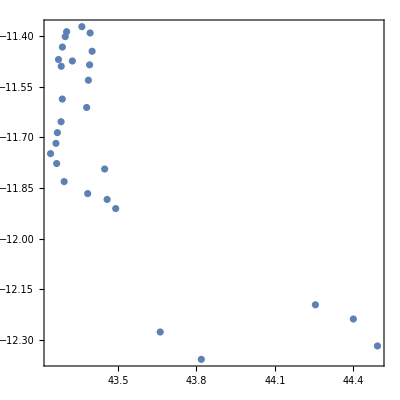

```mathematica
SeedRandom[42]
clustersNumber=35;
clusters=FindClusters[coords ,clustersNumber, Method->"KMeans"];
clustersCentroids={Mean[#[[All,1]]],Mean[#[[All,2]]]}&/@clusters;
clustersIndices=Table[Flatten[Position[coords,#]&/@i],{i,clusters}];
clusteredPopulations=Table[Total[pops[[#]]&/@i],{i,clustersIndices}];
(**)
ListPlot[clustersCentroids
,AspectRatio->1
,Frame->True
]
```

{CMYKColor[Rational[7, 10], Rational[1, 2], 0, 0],CMYKColor[0, Rational[9, 10], Rational[1, 2], 0],CMYKColor[0, 0, 0, 0],CMYKColor[1, 1, 1, 1],CMYKColor[0, 0, 0, 0]}

{56,2024,1345,1436,69,4236,36,0,61997,84,31016,67977,152070,351124,1922194,1105715,104056,15286,6679,43936,3401,1138,1242,63,420,5838,280,6}

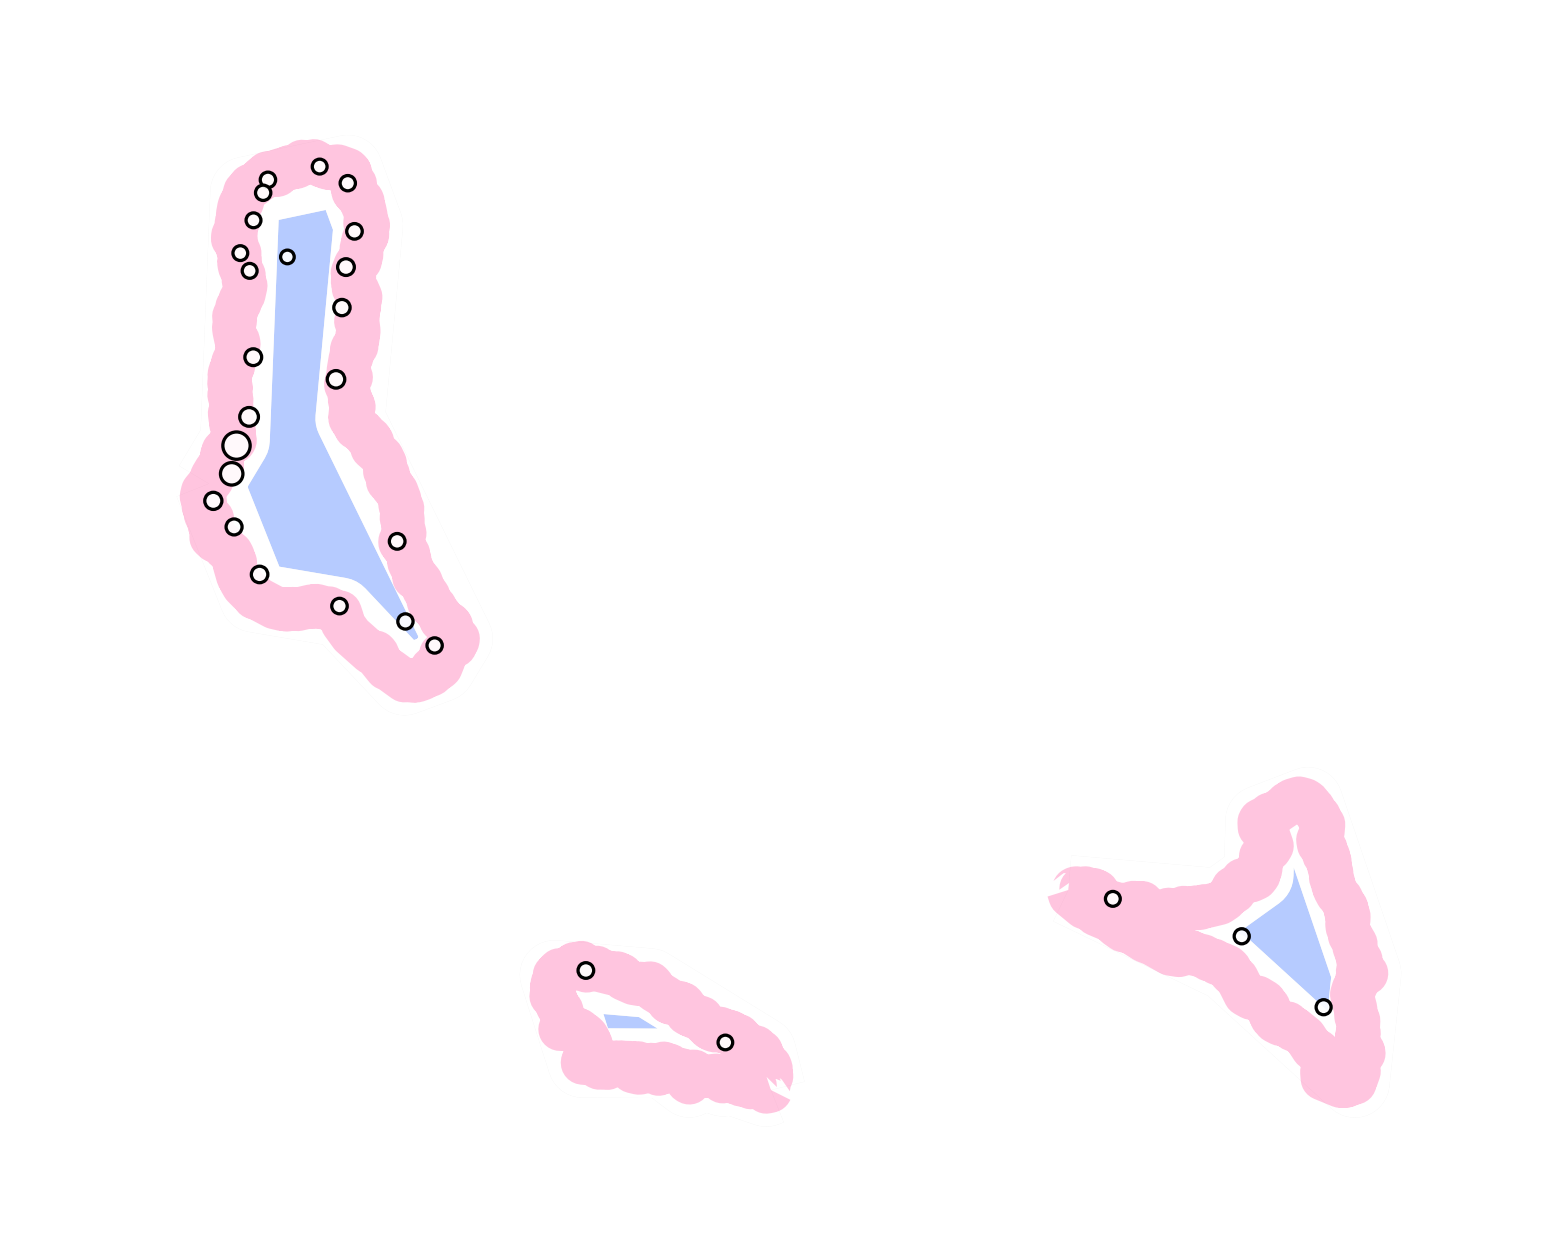

```mathematica
originalColorsValues={
{70,50,0,0},
{0,90,50,0},
{0,0,0,0},
{100,100,100,100},
{0,0,0,0}
};
colorPalette=CMYKColor[#[[1]]/100,#[[2]]/100,#[[3]]/100,#[[4]]/100]&/@originalColorsValues
latLongs=clustersCentroids;
populations=clusteredPopulations;
(**)
ordering=(Reverse/@latLongs)//Ordering//Reverse;
latLongs={latLongs[[ordering]][[All,1]]-.0,latLongs[[ordering]][[All,2]]-.075}//Transpose;
populations=populations[[ordering]]
(**)
sizes=Rescale[#,{Log[populations]//Min,Log[populations]//Max},{.05,2}]&/@Log[populations];
minMaxes={Min[#],Max[#]}&/@(latLongs//Transpose);
center=Mean/@minMaxes;
gridSize=Max[Abs[(#[[1]]-#[[2]])]&/@minMaxes]*.6;
(**)
GeoGraphics[{
(*Quiet[GeoPosition/@CityData[{All,countryName}]],*)
GeoStyling[EdgeForm[Directive[Opacity[1],Thickness[.05],Darker[colorPalette[[5]],.06]]],Opacity[.5],colorPalette[[1]]],
CountryData[countryName,"SchematicPolygon"],
GeoStyling[EdgeForm[Directive[Opacity[1],Thickness[.05],colorPalette[[5]]]],Opacity[.2],colorPalette[[3]]],
CountryData[countryName,"SchematicPolygon"],
GeoStyling[EdgeForm[Directive[Opacity[.25],Thickness[.020],colorPalette[[2]]]],Opacity[0],colorPalette[[5]]],
CountryData[countryName,"Polygon"]
}
,AspectRatio->Automatic
,Axes->False
(*,Background->Directive[{colorPalette[[5]],Opacity[1]}]*)
(*,Frame->True*)
,FrameStyle->Directive[colorPalette[[4]],Thickness[.0035]]
,FrameTicks->None
,FrameTicksStyle->White
(*,GridLines->Automatic
,GridLinesStyle->Directive[{Dashed,Thickness[.001],colorPalette[[4]]}]*)
,ImageSize->2000
(*,PlotRange->({#-gridSize,#+gridSize}&/@center)*)
,GeoBackground->None
,Prolog->{colorPalette[[1]],Opacity[.00005],EdgeForm[Directive[Opacity[.00000005],Thickness[.0025],colorPalette[[1]]]]}
,Epilog->{
White,
Opacity[.9],
EdgeForm[Directive[Thickness[.0015],Opacity[1],Black]],
DeleteCases[Disk[#[[1]],Log[1+0.0075+#[[2]]/250]]&/@Transpose[{latLongs,sizes//N}],Disk[Missing["NotAvailable"],_]],
Black,
Opacity[0],
Text[
Style[countryName,100,Lighter[colorPalette[[4]],.25],FontFamily->"Zapfino"
],{center[[1]]+.25gridSize,center[[2]]+gridSize*.25}]
}
]
```

```mathematica
latLongs=sampledPoints;
minMaxes={Min[#],Max[#]}&/@(latLongs//Transpose);
center=Mean/@minMaxes;
populations=Total/@totalPopulationDatasets[[All,1]];
(*sizes=Rescale[#,{Log[populations]//Min,Log[populations]//Max},{.05,2}]&/@Log[populations];*)
sizes=Rescale[#,{populations//Min,populations//Max},{0,1}]&/@populations;
gridSize=Max[Abs[(#[[1]]-#[[2]])]&/@minMaxes]*.75;
(**)
originalColorsValuesMap={
{70,100,0,0},
{40,60,0,0},
{50,100,0,0},
{100,100,100,100},
{0,0,0,0}
};
colorPaletteMap=Lighter[#,0]&/@(CMYKColor[#[[1]]/100,#[[2]]/100,#[[3]]/100,#[[4]]/100]&/@originalColorsValuesMap);
(**)
citiesNumber=Length[maleDatasets];
curve=PeanoCurve[3,DataRange->{{0,frameDimensions[[1]]},{0,frameDimensions[[2]]}}];
graphic=Graphics[{
Thickness[.01],LightGray,Opacity[.75],Dashing[0],BSplineCurve[curve[[1]],SplineDegree->1],
Thickness[.001],White,Opacity[1],Dashing[0],BSplineCurve[curve[[1]],SplineDegree->1]
}];
pointsNumber=Length[curve[[1]]];
sampledPoints=(curve[[1]]//DeleteDuplicates)[[Range[1,pointsNumber,Round[pointsNumber/citiesNumber]]]][[1;;citiesNumber]];
Show[graphic,ListPlot[sampledPoints,PlotStyle->PointSize[.015]],ImageSize->1500];
```

Transpose::nmtx: The first two levels of {sampledPoints,sampledPoints} cannot be transposed.

```mathematica
stepSize=4;
Table[
(*Subset Data*)
dataRange={i,i+stepSize};
subsetPopulations=SubsetPopulations[{aggregatedPopulations,aggregatedPopulationsAcrossNodes},dataRange];
pieChartFrames=ParallelMap[GeneratePieChartsAtTick[#,labels,maleMax+femaleMax]&,subsetPopulations[[1]]];
pieChartFrames=Table[{#[[1]],Sigmoid[#[[2]]]}&/@i,{i,pieChartFrames}];
{range,networkMatrix,vertexCoordinates}=CalculateNetworkParameters[sampledPoints,transitionsMatrix];
vertexShapeAndSizeFrames=ParallelMap[CalculateVertexScalers[{range,nodeScaler*.775},#]&,pieChartFrames];
networkFrames=ParallelTable[
GenerateNetworkFrames[vertexShapeAndSizeFrames[[j]],{vertexCoordinates,networkMatrix},{1,.0001,frameDimensions},{curve,curve},colorPaletteMap]
,{j,1,stepSize+1}];
ExportFrames[Show[graphic,#,ImageSize->frameDimensions]&/@networkFrames,dataRange,{outputFolder,outputNetworks,baseNetworks}];
(*Clear Memory*)
ClearSystemCache[];
Clear[dataRange,subsetPopulations,pieChartFrames,vertexShapeAndSizeFrames,networkFrames,range,networkMatrix,vertexCoordinates];
,{i,framesRange[[1]],framesRange[[2]]-stepSize,stepSize}];
```

## Final Frames

```mathematica
stepSize=4;
Table[
(*Subset Data*)
dataRange={i,i+stepSize};
{subsetPopulations,subsetPopulationsAccrossNodes}=SubsetPopulations[{aggregatedPopulations,aggregatedPopulationsAcrossNodes},dataRange];
(*Export Frames*)
fileNames=ParseFilenames[#,
{
outputFolder,
{outputPopCounts,outputBarCharts,outputFlow,outputNetworks},
{baseCounts,baseDays,baseBarCharts,basePopDyn,baseNetworks}
}]&/@Range[dataRange[[1]],dataRange[[2]]];
fullFrames=ParallelMap[GenerateAnimationFrameFromFiles[#]&,fileNames];
ExportFrames[fullFrames,dataRange,{outputFolder,outputFullFrames,baseFullFrames}];
(*Clear Memory*)
ClearSystemCache[];
Clear[dataRange,subsetPopulations,subsetPopulationsAccrossNodes,fileNames,fullFrames];
,{i,framesRange[[1]],framesRange[[2]]-stepSize,stepSize}];
```